## State model

```mathematica
SetDirectory[NotebookDirectory[]];
<<State`
?stateEquations
?outEquations
```

stateEquations[
	inVars_List,    (* input variable names, e.g. vS[t] *)
	stateVars_List, (* state variable names, e.g. vC1[t] *)
	equations_List  (* first-order ode and algebraic eqs, e.g. vC1'[t]==1/C1*iC1[t] *)
]
Returns the state equations as a list of replacement rules.
N.b. can handle some nonlinear systems.
N.b. a common mistake is to place the prime after the argument, but it should appear before, e.g. vC2'[t].
N.b. another common mistake is to use the assignment operator '=' instead of the boolean equals '==' in equations.
N.b. the arrangement of the equations (i.e. lhs/rhs) is immaterial.
N.b. for the output equations, use the function outEquations instead.
N.b. to linearize the returned state equations, use the function linearizeState.

outEquations[
	inVars_List,    (* input variable names, e.g. vS[t] *)
	stateVars_List, (* state variable names, e.g. vC1[t] *)
	outExps_List,   (* output expressions, e.g. vR2[t]+3*vC1[t] *)
	equations_List  (* first-order ode and algebraic eqs, e.g. vC1'[t]==1/C1*iC1[t] *)
]
Returns the rhs of the output equations as a list.
N.b. can handle some nonlinear systems.
N.b. can handle any expressions in outExps as long as they are expressed in terms of variables included in the
equations list. These are *not* limited to state variables! They can be primary or secondary and expressions thereof.
N.b. a common mistake is to place the prime after the argument, but it should appear before, e.g. vC2'[t].
N.b. another common mistake is to use the assignment operator '=' instead of the boolean equals '==' in equations.
N.b. the arrangement of the equations (i.e. lhs/rhs) is immaterial.
N.b. for the state equations, use the function stateEquations instead.
N.b. to linearize the returned output equations, use the function linearizeState.

```mathematica
inVars={
vs[t]
};
stateVars={
vce[t],
Tc2[t],
Tc1[t],
Tcl[t]
};
outExp=stateVars~Join~{
i1[t],
v1[t],
q2[t],
qr1[t]
};
equations={
vce'[t] == 1/ce*ice[t],
Tc1'[t] == 1/c1*qc1[t],
Tc2'[t] == 1/c2*qc2[t],
Tcl'[t] == 1/cl*qcl[t],
vrs[t]==irs[t]*rs,
vrm[t]==irm[t]*rm,
Tr1[t]==qr1[t]*r1,
Tr2[t]==qr2[t]*r2,
Tr3[t]==qr3[t]*r3,
q2[t]==v1[t]*i1[t],
T2[t]==-1/α*v1[t],
ice[t]==irs[t]-irm[t],
irm[t]==i1[t],
qc1[t]==-q2[t]-qr1[t]-qr2[t],
qc2[t]==q2[t]+qr1[t]-qr3[t],
qcl[t]==qr2[t],
vrs[t]==vs[t]-vce[t],
vrm[t]==vce[t]-v1[t],
Tr1[t]==Tc1[t]-Tc2[t],
Tr2[t]==Tc1[t]-Tcl[t],
Tr3[t]==Tc2[t],
T2[t]==Tc1[t]-Tc2[t]
};
ass={rs,r1,r2,r3,rm,cl,c1,c2,ce}//Thread[#>0]&
n=Length[stateVars];
m=Length[outExp];
r=Length[inVars];
```

{rs>0,r1>0,r2>0,r3>0,rm>0,cl>0,c1>0,c2>0,ce>0}

```mathematica
stateEqSol=stateEquations[inVars,stateVars,equations]//Flatten;
stateEqSol//TableForm
stateEqList = stateVars//D[#,t]&//ReplaceAll[#,stateEqSol]&;
```

vce'[t]→-(α Tc1[t])/(ce rm)+(α Tc2[t])/(ce rm)-((rm+rs) vce[t])/(ce rm rs)+vs[t]/(ce rs)
Tc2'[t]→Tc1[t]/(c2 r1)-(α^2 Tc1[t]^2)/(c2 rm)+(-(r1 rm+r3 rm)/(c2 r1 r3 rm)+(2 α^2 Tc1[t])/(c2 rm)) Tc2[t]-(α^2 Tc2[t]^2)/(c2 rm)+(-(α Tc1[t])/(c2 rm)+(α Tc2[t])/(c2 rm)) vce[t]
Tc1'[t]→(-1/(c1 r1)-1/(c1 r2)) Tc1[t]+(α^2 Tc1[t]^2)/(c1 rm)+(1/(c1 r1)-(2 α^2 Tc1[t])/(c1 rm)) Tc2[t]+(α^2 Tc2[t]^2)/(c1 rm)+Tcl[t]/(c1 r2)+((α Tc1[t])/(c1 rm)-(α Tc2[t])/(c1 rm)) vce[t]
Tcl'[t]→Tc1[t]/(cl r2)-Tcl[t]/(cl r2)

```mathematica
outEqList = outEquations[inVars,stateVars,outExp,equations]
```

{vce[t],Tc2[t],Tc1[t],Tcl[t],(α Tc1[t])/rm-(α Tc2[t])/rm+vce[t]/rm,-α Tc1[t]+α Tc2[t],-(α^2 Tc1[t]^2)/rm+(2 α^2 Tc1[t] Tc2[t])/rm-(α^2 Tc2[t]^2)/rm+(-(α Tc1[t])/rm+(α Tc2[t])/rm) vce[t],Tc1[t]/r1-Tc2[t]/r1}

```mathematica
nsys=NonlinearStateSpaceModel[{stateEqList,outEqList},stateVars,inVars]
```

-(α Tc1[t])/(ce rm)+(α Tc2[t])/(ce rm)-((rm+rs) vce[t])/(ce rm rs)+vs[t]/(ce rs)Tc1[t]/(c2 r1)-(α^2 Tc1[t]^2)/(c2 rm)+(-(r1 rm+r3 rm)/(c2 r1 r3 rm)+(2 α^2 Tc1[t])/(c2 rm)) Tc2[t]-(α^2 Tc2[t]^2)/(c2 rm)+(-(α Tc1[t])/(c2 rm)+(α Tc2[t])/(c2 rm)) vce[t](-1/(c1 r1)-1/(c1 r2)) Tc1[t]+(α^2 Tc1[t]^2)/(c1 rm)+(1/(c1 r1)-(2 α^2 Tc1[t])/(c1 rm)) Tc2[t]+(α^2 Tc2[t]^2)/(c1 rm)+Tcl[t]/(c1 r2)+((α Tc1[t])/(c1 rm)-(α Tc2[t])/(c1 rm)) vce[t]Tc1[t]/(cl r2)-Tcl[t]/(cl r2)vce[t]Tc2[t]Tc1[t]Tcl[t](α Tc1[t])/rm-(α Tc2[t])/rm+vce[t]/rm-α Tc1[t]+α Tc2[t]-(α^2 Tc1[t]^2)/rm+(2 α^2 Tc1[t] Tc2[t])/rm-(α^2 Tc2[t]^2)/rm+(-(α Tc1[t])/rm+(α Tc2[t])/rm) vce[t]Tc1[t]/r1-Tc2[t]/r1vce[t]Tc2[t]Tc1[t]Tcl[t] 4188NoneNoneFalseFalseFalse{vs[t]}Automatic

## Simulate

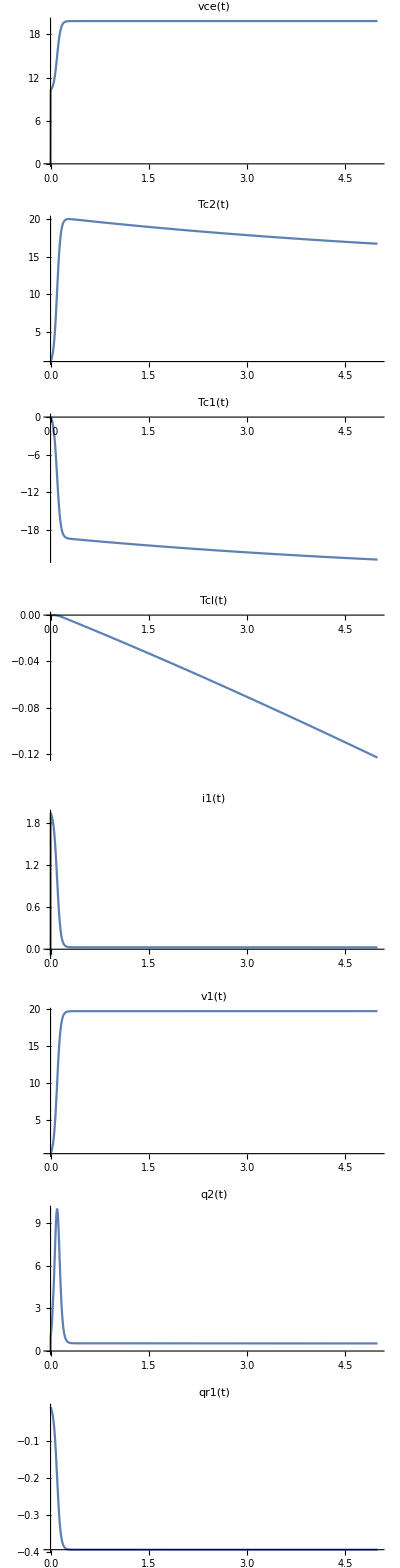

```mathematica
tlow=0;
thigh=5;
(*sb[T_]:=1.33450*10^-2+-5.37574*10^-5*T+7.42731*10^-7*T^2+-1.27141*10^-9*T^3;*)
params={ (* these need work *)
rs->5,
r1->100,
r2->200,
r3->100,
rm-> 5,
cl->.001*10^-3*4.2*10^6,
c1->.01*(.03*.03*.002)*3*10^6,
c2->.01*(.03*.03*.002)*3*10^6,
ce->10*10^-6,
α->.5
};
nsysResponse=OutputResponse[{nsys/.params,{0,1,0,0}},20*UnitStep[t],{t,tlow,thigh}];
Table[
Plot[nsysResponse[[i]],{t,tlow,thigh},PlotRange->All,PlotLabel->outExp[[i]]],
{i,1,m}
]//GraphicsColumn[#,ImageSize->Full]&
```

## Printing to Matlab (needs work)

The issue I’m having is getting Matlab to automatically generate a function file so I can ode45 it.
Once this is working, incorporate it into State as a function.

```mathematica
<<ToMatlab`
stateMatRep=Thread[stateVars->Table["x("<>ToString[i]<>")",{i,1,Length[stateVars]}]]~Join~
Thread[inVars->Table["u("<>ToString[i]<>")",{i,1,Length[inVars]}]]
myToMatlab[exp_]:=(exp/.stateMatRep//Map[ReplaceAll[#,x_[t_]:>x]&,#]&//ReplaceAll[#,α->a]&//ToMatlab//ToString);

matlabVars=stateEqList//Variables//ReplaceAll[#,α->a]&//Complement[#,stateVars~Join~inVars]&//Map[ReplaceAll[#,x_[t_]:>x]&,#]&;

(*{{"syms"}~Join~matlabVars}//Grid*)
For[i=1,i≤Length[matlabVars],i++,(matlabVars[[i]]//ToString)<>"=1; % dummy"//Print]
Length[stateVars]//Print["f=sym('f',["<>ToString[#]<>",1]);"]&;
Length[stateVars]//Print["x=sym('x',["<>ToString[#]<>",1]);"]&;
Length[inVars]//Print["u=sym('u',["<>ToString[#]<>",1]);"]&;

For[i=1,i≤Length[stateVars],i++,"f("<>ToString[i]<>")="<>(myToMatlab[stateEqList[[i]]])//Print]
```

{vce[t]→x(1),Tc1[t]→x(2),Tc2[t]→x(3),Tcl[t]→x(4),vs[t]→u(1)}

a=1; % dummy
c1=1; % dummy
c2=1; % dummy
ce=1; % dummy
cl=1; % dummy
r1=1; % dummy
r2=1; % dummy
r3=1; % dummy
rm=1; % dummy
rs=1; % dummy
f=sym('f',[4,1]);
x=sym('x',[4,1]);
u=sym('u',[1,1]);
f(1)=(-1).*x(2).*a.*ce.^(-1).*rm.^(-1)+x(3).*a.*ce.^(-1).*rm.^(-1)+u(1) ...\n  .*ce.^(-1).*rs.^(-1)+(-1).*x(1).*ce.^(-1).*rm.^(-1).*rs.^(-1).*( ...\n  rm+rs);\n
f(2)=x(3).*c1.^(-1).*r1.^(-1)+x(4).*c1.^(-1).*r2.^(-1)+x(1).*(x(2).*a.* ...\n  c1.^(-1).*rm.^(-1)+(-1).*x(3).*a.*c1.^(-1).*rm.^(-1))+x(2).*(c1.^( ...\n  -1).*r1.^(-1).*((-1).*r1+(-1).*r2).*r2.^(-1)+(-2).*x(3).*a.^2.* ...\n  c1.^(-1).*rm.^(-1))+x(2).^2.*a.^2.*c1.^(-1).*rm.^(-1)+x(3).^2.* ...\n  a.^2.*c1.^(-1).*rm.^(-1);\n
f(3)=x(3).*c2.^(-1).*r1.^(-1).*((-1).*r1+(-1).*r3).*r3.^(-1)+x(1).*(( ...\n  -1).*x(2).*a.*c2.^(-1).*rm.^(-1)+x(3).*a.*c2.^(-1).*rm.^(-1))+x(2) ...\n  .*(c2.^(-1).*r1.^(-1)+2.*x(3).*a.^2.*c2.^(-1).*rm.^(-1))+(-1).*x( ...\n  2).^2.*a.^2.*c2.^(-1).*rm.^(-1)+(-1).*x(3).^2.*a.^2.*c2.^(-1).* ...\n  rm.^(-1);\n
f(4)=x(2).*cl.^(-1).*r2.^(-1)+(-1).*x(4).*cl.^(-1).*r2.^(-1);\n